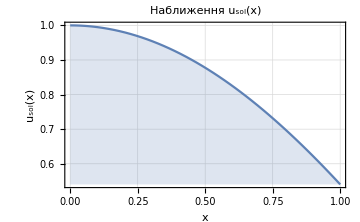
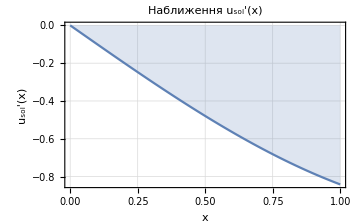

‖u_sol‖_0=0.852833												‖u_sol‖_1=1.

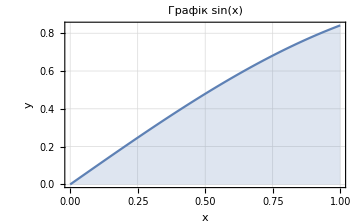
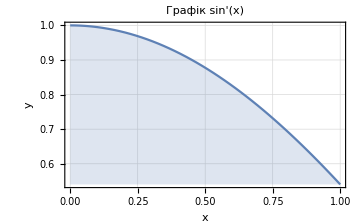

################################################[----FEM n=2 h=1/2----]################################################

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression 1+j cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

K=(4. | -2.
-2. | 2.)

F={0.429726,-0.674561}

q={-0.122417,-0.459698}

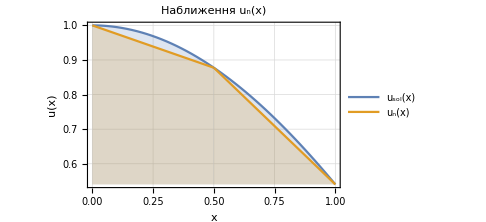
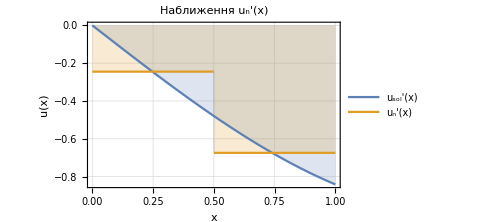

‖u_n‖_0=0.835062 ‖u-u_n‖_0=0.173193 ((‖u - SubscriptBox[u, n]‖)_0)/((‖SubscriptBox[u, n]‖)_0)100%=20.7402%                     ‖u_n‖_1=0.977147 ‖u-u_n‖_1=0.212564 ((‖u - SubscriptBox[u, n]‖)_1)/((‖SubscriptBox[u, n]‖)_1)100%=21.7535%

```mathematica
a=0;b=1;f[x_]:=Cos[x];
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = 1; u1 = -Sin[1];
$MaxPiecewiseCases=700;
(*Точний розвязок диф рівняння*)
Subscript[u, sol]=NDSolveValue[{-(μ'[x]*u'[x]+μ[x] u''[x])+β[x] u'[x]+σ[x] u[x]==f[x],u[a]==u0,u'[b]==u1},u,{x,a,b}];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x],{x,a,b},FrameLabel->{"x ","u_sol(x) "},PlotLabel->Style[Framed["Наближення u_sol(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Subscript[u, sol]'[x],{x,a,b},FrameLabel->{"x ","u_sol'(x) "},PlotLabel->Style[Framed["Наближення u_sol'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=√NIntegrate[Subscript[u, sol][x]^2,{x,a,b}];
Subscript[norma2u, sol]=√NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}];
Print[Subscript[plot1u, sol],"  ",  Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
resfunc[x_] = Sin[x];
Print[Plot[y=resfunc[x] ,{x,a,b}, FrameLabel->{"x ","y "},PlotLabel->Style[Framed["Графік sin(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium], "   ", Plot[y=resfunc'[x],{x,a,b}, FrameLabel->{"x ","y "},PlotLabel->Style[Framed["Графік sin'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium]];
(*Функції Куранта*)
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],i≠ 1 && i≠n+1}, 
{Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,w⟦k⟧<x≤1}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,0≤x<w⟦i⟧}}], i==n+1}
}]];
n = 2;
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];
Print["################################################[----FEM n=",n," h=",h,"----]################################################"];
matrixK = 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(μ[x]*D[ϕ[x,j+1], x]*D[ϕ[x,i+1], x]+β[x]*D[ϕ[x,j+1], x]*ϕ[x,i+1]+σ[x]*ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["K=",MatrixForm[matrixK]];
F = Table[NIntegrate[f[x]*ϕ[x,i+1],{x,a,b}]+u1*μ[b]*ϕ[b,i+1], {i,1,n}];
Print["F=",F];
q = LinearSolve[matrixK,F];
Print["q=",q];
Subscript[u, n][x_]:=u0+∑_(i=1)^n q[[i]]*ϕ[x,i+1];
difference1 = Plot[{Subscript[u, sol][x], Subscript[u, n][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
difference2 = Plot[{Subscript[u, sol]'[x], Subscript[u, n]'[x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Print[difference1, "  ", difference2];
Subscript[norma1u, n]=√NIntegrate[Subscript[u, n][x]^2,{x,a,b}];
Subscript[norma2u, n]=√(NIntegrate[(Subscript[u, sol][x]^2),{x,a,b}]-NIntegrate[(Subscript[u, n][x]^2),{x,a,b}]);
Subscript[norma1u, n1]=√NIntegrate[(Subscript[u, n][x])^2+(Subscript[u, n]'[x])^2,{x,a,b}];
Subscript[norma2u, n1]=√(NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}]-NIntegrate[(Subscript[u, n][x])^2+(Subscript[u, n]'[x])^2,{x,a,b}]);
Print["‖u_n‖_0=",Subscript[norma1u, n], " ‖u-u_n‖_0=", Subscript[norma2u, n], " ((‖u - SubscriptBox[u, n]‖)_0)/((‖SubscriptBox[u, n]‖)_0)100%=", (Subscript[norma2u, n]/Subscript[norma1u, n])*100, "%                     ‖u_n‖_1=",Subscript[norma1u, n1], " ‖u-u_n‖_1=", Subscript[norma2u, n1], " ((‖u - SubscriptBox[u, n]‖)_1)/((‖SubscriptBox[u, n]‖)_1)100%=", (Subscript[norma2u, n1]/Subscript[norma1u, n1])*100,"%"];
```